{{y→InterpolatingFunction[…]}}

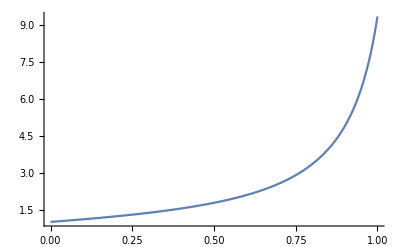

```mathematica
s=NDSolve[{y'[x]==y[x]^2-x,y[0]==1},y,{x,0,1}]
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

```mathematica
y[1]/.s
```

{9.35382}

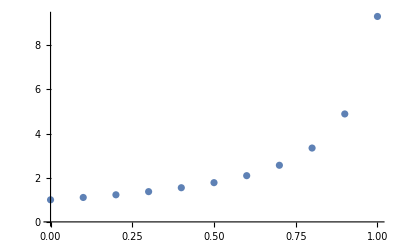

```mathematica
Clear[y]
f[x_,y_]:=y^2-x
y[0]=1;
h:=0.1;
Do[k1= f[h* n,y[n]];
k2= f[h *(n+(1/2)),y[n]+k1* (h/2)];
k3= f[h *(n+(1/2)),y[n]+k2* (h/2)];
k4= f[h *(n+1),y[n]+k3* h];
y[n+1]=y[n]+(h/6) (k1+2*k2+2*k3+k4),{n,0,10}]
a=ListPlot[Table[{n*h,y[n]},{n,0,10}]]
```

```mathematica
y[10]
```

9.29753

```mathematica
(The difference of the results using numerical solve, and runge-kutta)
```

```mathematica
difference = 9.353820831189541 -9.29753187663837
```

0.056289

```mathematica
(using IE method)
```

IE method using

```mathematica
Clear[y, k1, k2, k3, k4]
```

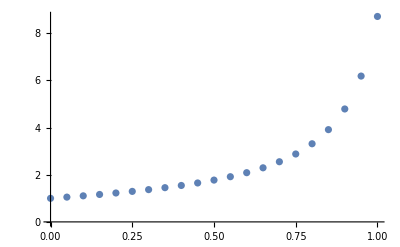

```mathematica
f[x_,y_]:=y^2-x
y[0]=1;
h:=0.05;
Do[k1=h f[h n,y[n]];
k2=h f[h (n+1),y[n]+k1];
y[n+1]=y[n]+.5 (k1+k2),{n,0,20}]
c=ListPlot[Table[{n*h,y[n]},{n,0,20}]]
```

```mathematica
y[20]
```

8.71523

```mathematica
(diff between actual and IE)
```

actual and between diff IE

```mathematica
differenceie = 9.29753187663837 - 8.715234970278456
```

0.582297

```mathematica
(E Method)
```

ⅇ Method

```mathematica
Clear[y, k1,k2]
```

```mathematica
f[x_,y_]:=y^2-x
```

1

0.02

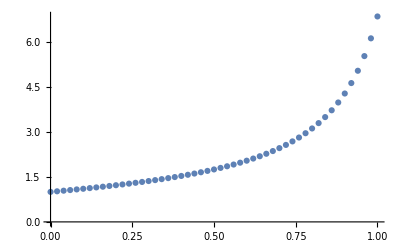

```mathematica
y[0]=1
h=.02
Do[y[n]=y[n-1]+h*f[(n-1)*h,y[n-1]],{n,1,50}]
d=ListPlot[Table[{n*h,y[n]},{n,0,50}]]
```

```mathematica
y[50]
```

6.84859

```mathematica
(differenceE and actual)
```

actual and differenceE

```mathematica
differenceE = 9.353820831189541-6.84858709456998
```

2.50523

```mathematica
(Clearly runge-kutta is the most accurate)
```

Clearly runge-accurate is kutta most the

```mathematica
(All the graphs together)
```

All graphs the together

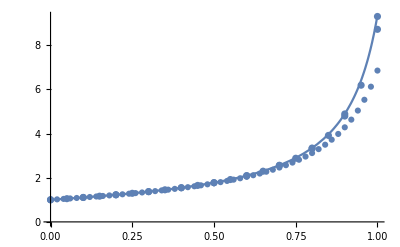

```mathematica
Show[a,b,c,d]
```